```mathematica
a={{2010,3070000},{2011,3070000},{2012,2840000},{2013,2764000},{2014,2732000},{2015,2732000},{2016,2726000},{2017,2498000},{2018,2358000},{2019,2236000},{2020,1993000},{2021,1814000},{2022,1649000}}
```

{{2010,3070000},{2011,3070000},{2012,2840000},{2013,2764000},{2014,2732000},{2015,2732000},{2016,2726000},{2017,2498000},{2018,2358000},{2019,2236000},{2020,1993000},{2021,1814000},{2022,1649000}}

```mathematica
(* year 2011 has no circulation data, previous year circulation employed for 2011 *)
```

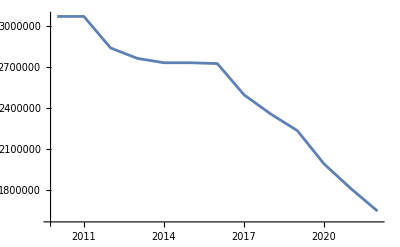

```mathematica
ListPlot[a,Joined->True]
```

```mathematica
b={{2010,100000},{2011,170000},{2012,250000},{2013,335000},{2014,390000},{2015,449000},{2016,501000},{2017,558000},{2018,620000},{2019,698000},{2020,760000},{2021,797000},{2022,823000}}
```

{{2010,100000},{2011,170000},{2012,250000},{2013,335000},{2014,390000},{2015,449000},{2016,501000},{2017,558000},{2018,620000},{2019,698000},{2020,760000},{2021,797000},{2022,823000}}

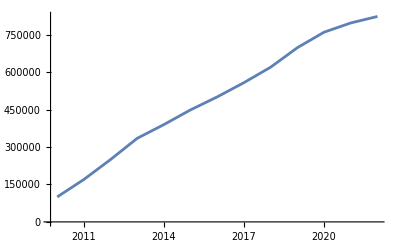

```mathematica
ListPlot[b,Joined->True]
```

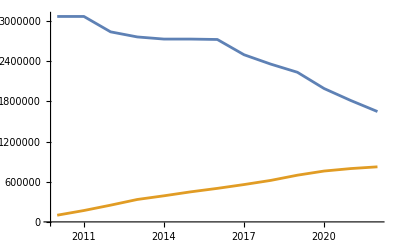

```mathematica
ListPlot[{a,b},Joined->True]
```

```mathematica
pc=5500
```

5500

```mathematica
ec=4277
```

4277

```mathematica
a2=Transpose[a]
```

{{2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022},{3070000,3070000,2840000,2764000,2732000,2732000,2726000,2498000,2358000,2236000,1993000,1814000,1649000}}

```mathematica
a3={a2[[1]],pc*a2[[2]]}
```

{{2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022},{16885000000,16885000000,15620000000,15202000000,15026000000,15026000000,14993000000,13739000000,12969000000,12298000000,10961500000,9977000000,9069500000}}

```mathematica
a4=Transpose[a3]
```

{{2010,16885000000},{2011,16885000000},{2012,15620000000},{2013,15202000000},{2014,15026000000},{2015,15026000000},{2016,14993000000},{2017,13739000000},{2018,12969000000},{2019,12298000000},{2020,10961500000},{2021,9977000000},{2022,9069500000}}

```mathematica
b2=Transpose[b]
```

{{2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022},{100000,170000,250000,335000,390000,449000,501000,558000,620000,698000,760000,797000,823000}}

```mathematica
b3={b2[[1]],ec*b2[[2]]}
```

{{2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022},{427700000,727090000,1069250000,1432795000,1668030000,1920373000,2142777000,2386566000,2651740000,2985346000,3250520000,3408769000,3519971000}}

```mathematica
b4=Transpose[b3]
```

{{2010,427700000},{2011,727090000},{2012,1069250000},{2013,1432795000},{2014,1668030000},{2015,1920373000},{2016,2142777000},{2017,2386566000},{2018,2651740000},{2019,2985346000},{2020,3250520000},{2021,3408769000},{2022,3519971000}}

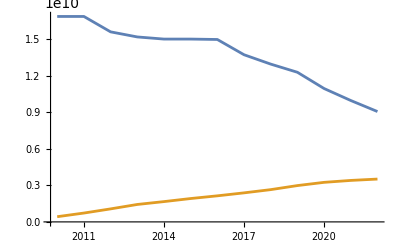

```mathematica
ListPlot[{a4,b4},Joined->True]
```

```mathematica
c={a2[[1]],a3[[2]]+b3[[2]]}
```

{{2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022},{17312700000,17612090000,16689250000,16634795000,16694030000,16946373000,17135777000,16125566000,15620740000,15283346000,14212020000,13385769000,12589471000}}

```mathematica
c4=Transpose[c]
```

{{2010,17312700000},{2011,17612090000},{2012,16689250000},{2013,16634795000},{2014,16694030000},{2015,16946373000},{2016,17135777000},{2017,16125566000},{2018,15620740000},{2019,15283346000},{2020,14212020000},{2021,13385769000},{2022,12589471000}}

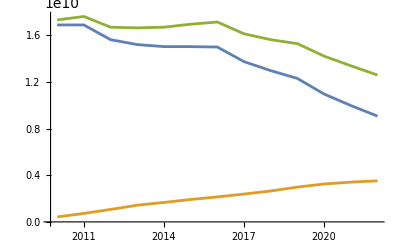

```mathematica
ListPlot[{a4,b4,c4},Joined->True]
```

```mathematica
MatrixForm[a]
```

(2010 | 3070000
2011 | 3070000
2012 | 2840000
2013 | 2764000
2014 | 2732000
2015 | 2732000
2016 | 2726000
2017 | 2498000
2018 | 2358000
2019 | 2236000
2020 | 1993000
2021 | 1814000
2022 | 1649000)

```mathematica
MatrixForm[b]
```

(2010 | 100000
2011 | 170000
2012 | 250000
2013 | 335000
2014 | 390000
2015 | 449000
2016 | 501000
2017 | 558000
2018 | 620000
2019 | 698000
2020 | 760000
2021 | 797000
2022 | 823000)